# Non classical light and quadratures

This chapter introduces the concept of nonclassical light, identifying quantum states of the electromagnetic field that cannot be described by classical physics. It presents several key signatures of non-classicality, including sub-Poissonian photon statistics, photon antibunching, and quadrature squeezing—each indicating departures from classical behavior. The chapter explores how these features manifest in specific states like squeezed vacuum and Schrödinger-cat states, and discusses experimental techniques for generating and detecting nonclassical light, such as parametric down-conversion and homodyne detection. These tools and phenomena form the foundation for advanced applications in quantum optics, metrology, and quantum information.

### Key concepts

Quadrature squeezing and squeeze operator

Properties of squeezed states of light

Homodyne detection

Schrodinger cat states

Two-mode squeezed states

## Quadrature squeezing

### Squeezing definition

If two operators Â and B̂ have the commutation relation  it is a well known fact that 

A state of a system is squeezed if one of these holds:
or  (of course both cannot hold otherwise uncertainty principle is violated) 
For quadrature operators X_1 and X_2 ,  so squeezing exists if  
 or  
We know coherent states and also the vacuum , have both quadrature variances of 1/4 and satisfy the uncertainty equality. In the figure below, we can see a representation of squeezing in the shaded regions, one quadrature noise can go below vacuum(“squeezed”) but the other one increases. Ideal squeezed states lie in the hyperbola (they satisfy the equality) but in general squeezed states can be anywhere in the shaded regions.

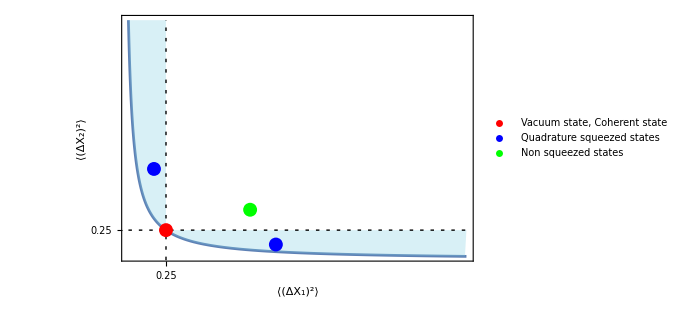

```mathematica
Legended[Show[Plot[1/(16 x),{x,1/32,2},PlotRange->Full,FrameTicks->{{{0.25},None},{{0.25},None}},Epilog->{{Dashing[{0.005,0.01}],Line[{{1/32,0.25},{2,0.25}}]},{Dashing[{0.005,0.01}],Line[{{0.25,0},{0.25,2}}]},{Red,PointSize[0.02],Point[{0.25,0.25}]},{Blue,PointSize[0.02],Point[{0.18,0.76}],Point[{0.89,0.13}]},{Green,PointSize[0.02],Point[{0.74,0.42}]}}],Graphics[{{RGBColor[0.5,0.81,0.89],Opacity[0.3],Polygon[Join[Table[{x,1/(16 x)},{x,1/32,2,0.01}],{{2,0.25},{0.25,0.25},{0.25,2}}  ]]}}],FrameLabel->(Style[#,14]&)/@{"⟨(ΔX_1)^2⟩","⟨(ΔX_2)^2⟩"},Frame->True,ImageSize->500],PointLegend[{Red,Blue,Green},{"Vacuum state, Coherent state","Quadrature squeezed states","Non squeezed states"},LegendFunction->"Panel",LabelStyle->16,LegendMarkerSize->16]]
```

Also for a coherent state with a complex α it holds   and   :

```mathematica
αc = RandomComplex[]
```

0.32976+0.149847 ⅈ

```mathematica
(QuantumMeasurementOperator[N[#]]@ coherent[αc])["Mean"]& /@ QuadratureOperators[]
```

{0.32976,0.149847}

Phase space picture its a circle with center (Re(α), Im(α)):

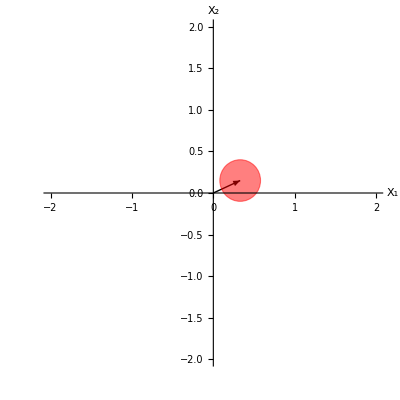

```mathematica
Graphics[
{Arrow[{{0,0},{Re[αc],Im[αc]}}],
EdgeForm[Dashed],Directive[Red],Background->LightBlue,Opacity[0.5],
Disk[{Re[αc],Im[αc]},
Chop[OperatorVariance[coherent[αc],#]&/@QuadratureOperators[]]]},
Axes->True,
AxesOrigin->{0,0},
AxesLabel->(Style[#1,14]&)/@{"X_1","X_2"},
PlotRange->{{-2,2},{-2,2}}]
```

Squeezed states are called non-classical because using the Glauber-Sudarshan P function it can be showed if one quadrature variance is < 1/4 implies P(α) is non negative at least in some phase space region. It is also useful to introduce an angle dependent quadrature operator  X̂(θ) = 1/2(â  e^(-ⅈ θ)+(â)^† e^(ⅈ θ))

```mathematica
Xθ := QuantumOperator[1/2(a ⅇ^(-ⅈ θ)+SuperDagger[a] ⅇ^(ⅈ θ)),"Parameters"->θ];
```

X(0) = X_1 and X(π/2) = X_2

```mathematica
Thread[{Xθ[0] , Xθ[Pi/2]}==QuadratureOperators[]]
```

{True,True}

A squeezing  s parameter is defined s(θ) = 4 ⟨(ΔX(θ))^2⟩ - 1, squeezing exists if for some angle -1≤ s(θ) <0

```mathematica
sParameter[ψ_QuantumState,θ_]:= 4 OperatorVariance[ψ,Xθ[θ]]-1
```

### Squeezed operator and squeezed vacuum

The unitary squeeze operator is defined as  can be understood as a two photon generalization of displacement operator, where ξ is a complex number ξ = r e^(ⅈ θ), r is called the squeeze parameter 0 ≤ r ≤ ∞

Squeeze operator in Wolfram Quantum Framework:

```mathematica
SqueezeOperator[ξ]
```

QuantumOperator[…]

This properties should hold:

```mathematica
SetFockSpaceSize[25];
ξ1 = RandomReal[{0.3,0.8}]Exp[ⅈ RandomReal[{0,2π}]];
```

Since we are working in a truncated Fock space size, some algebraic properties can work better numerically in a particular operator ordering, here we use weak ordering:

```mathematica
Chop[SqueezeOperator[ξ1,"Ordering"->"Weak"]@SqueezeOperator[-ξ1,"Ordering"->"Weak"]] == QuantumOperator["I"[$FockSize]]
```

True

```mathematica
SqueezeOperator[ξ1,"Ordering"->"Weak"]["UnitaryQ"]
```

True

Using Baker-Hausdorff formula   we get  properties   and   
however, in the implementation do not hold exactly because they rely on the commutator [a, a^†] = 1 that is not exact in a truncated Fock space.
Squeezed operator is more numerically sensitive to error because it is a two photon operator ,  the Fock size space have to scale  to larger sizes compared to displacement operator to get accurate numeric results

Squeezed vacuum state   :

```mathematica
squeezevacuum = SqueezeOperator[ξ1][];
```

The squeeze operator does not change the expectations of X1 and X2

```mathematica
(SuperDagger[squeezevacuum]@N[#]@ squeezevacuum)["Scalar"] & /@ QuadratureOperators[]
```

{0,0}

But the variances we see one got squeezed ( less than 0.25) and the other one increased:

```mathematica
Chop @ OperatorVariance[squeezevacuum,#]& /@ QuadratureOperators[]
```

{0.563105,0.226476}

It can be derived using the properties of Ŝ on a and a^† that 
and

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{0.563105,0.226476}

When θ = 0 the expressions reduce to  
For this case its clearly seen one quadrature gets “squeezed” while the other increases so it maintains the uncertainty principle, also in this case (θ = 0)  the inequality is saturated ( the product of uncertainties equals 1/16 = 0.0625). This is different from a coherent state or Fock state that also saturate the inequality, but they had the same value for the uncertainties in X_1 and X_2.

```mathematica
ξ1 = RandomReal[{0,1.5}];
squeezevacuum = SqueezeOperator[ξ1][];
```

```mathematica
variances = (OperatorVariance[squeezevacuum,#]//Chop)& /@ QuadratureOperators[]
```

{0.089344,0.699544}

```mathematica
1/4{Exp[-2ξ1],Exp[2ξ1]}
```

{0.089344,0.699544}

Phase space representation for the cases with θ = 0 and θ=π (not to scale for visual purposes), in these cases the squeezing is along the axes of X_1 or X_2 describing error ellipses:

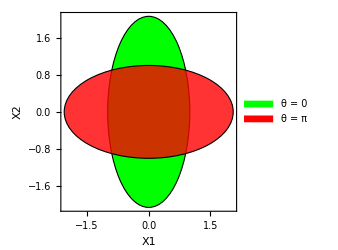

```mathematica
With[{dx =1, dy =variances[[2]]/variances[[1]]//Log}, 
Legended[
Graphics[{
EdgeForm[Dashed],Green,Disk[{0,0},{dx,dy}],
Opacity[0.8],Red,Disk[{0,0},{dy,dx}]},
Axes->True,
Frame->True,
ImageSize->250,
AxesLabel->{"X1","X2"}],
SwatchLegend[{Green,Red},{"θ = 0", "θ = π"}]]]
```

For a general  ξ = r e^ⅈθ we can defined rotated quadrature operators  Y_1 = cos(θ/2)X_1+ sin(θ/2)X_2  and Y_2= -sin(θ/2)X_1+cos(θ/2)X_2
such that the variances are calculated along the rotated quadrature axes. Because of that reason the value of the variances are  ⟨Δ Y_1 ⟩^2 = 1/4 e^(-2r)    ⟨Δ Y_2 ⟩^2 = 1/4 e^(2r) .  At  θ = 0   Y_1 and Y_2 reduce to X_1 and X_2

```mathematica
YOperators :=( QuantumOperator[#,"Parameters"->θ]& )/@( RotationMatrix[-θ/2].QuadratureOperators[])
```

```mathematica
Through[YOperators[0]] == QuadratureOperators[]
```

True

```mathematica
ξ1 = RandomComplex[{1+ⅈ}];
squeezevacuum = SqueezeOperator[ξ1][];
```

```mathematica
variances = With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, OperatorVariance[squeezevacuum,#]& /@ Through[YOperators[θ1]]]//Chop
```

{0.0337699,1.83625}

```mathematica
1/4{Exp[-2r],Exp[2r]}/. r->Abs[ξ1]
```

{0.0339031,1.84349}

Phase space picture are rotated ellipses with angle of rotation θ/2  (the dashed lines represent the Y1 and Y2 quadrature axes)

```mathematica
Module[
{θ1=Arg[ξ1],dx =1,dy}, 
dy =1/(Divide @@ variances );
Graphics[{
EdgeForm[Thick],Green,
Rotate[Disk[{0,0},{dx,dy}],θ1/2],
Black,Dashed,
Line[Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],
Line[Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
]},
Axes->True,
Frame->True,
ImageSize->Medium,
FrameTicks->None,
AxesLabel->{"X1","X2"}]
]
```

-Graphics-

Visualization of the ellipse errors , the product of the variances of X_1 and X_2 only equals the uncertainty limit(1/16)  when the ellipses are alligned with the X_1 and X_2 axes:

```mathematica
Manipulate[
Module[
{dx =1/4 Exp[-2r],dy =1/4Exp[2r]}, 
Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{0,0},{dx,dy}],θ1/2],
Black,Dashed,
Line[Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],
Line[Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]],
Text[Framed[(ΔX1)^2 == 1/4(Cosh[r]^2+Sinh[r]^2-2Sinh[r]Cosh[r]Cos[θ1]),
FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.8,0.85}],Text[Framed[(ΔX2)^2 == 1/4(Cosh[r]^2+Sinh[r]^2+2Sinh[r]Cosh[r]Cos[θ1]),
FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.8,0.55}],Text[Framed[(ΔX1)^2(ΔX2)^2 == 1/16((Cosh[r]^2+Sinh[r]^2)^2-(2Sinh[r]Cosh[r]Cos[θ1])^2),FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.75,-0.75}]
},
Axes->True,
ImageSize->Medium,
AxesLabel->{"X1","X2"},
PlotRange->{{-1,1},{-1,1}},
PlotLabel->"Quadratures of a squeezed vacuum state |ξ⟩"]]
,{{r,0,"Modulus r"},0,1},{{θ1,0,"Argument θ"},0,2π},SaveDefinitions->True]
```

### Squeezed coherent state and displaced squeezed state

A squeezed coherent state is obtained applying the squeeze operator to a coherent state

```mathematica
SetFockSpaceSize[80];
```

```mathematica
{αcoh,ξ1} = RandomReal[{0.2,1.5},2]Exp[I RandomReal[{0,2π},2]];
```

```mathematica
squeezeCoh = SqueezeOperator[ξ1]@ DisplacementOperator[αcoh][];
```

Mean number of photons has this analytical expression:

```mathematica
(QuantumMeasurementOperator[SuperDagger[a]@a]@squeezeCoh)["Mean"]
```

5.58494

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Abs[αcoh]^2(Cosh[r]^2+Sinh[r]^2)+Sinh[r]^2-2Re[(αcoh^2 Exp[-I θ])]Cosh[r]Sinh[r]]
```

5.58494

Another state  that is more general than squeezed vacuum is the displaced squeezed state is defined as: |α, ξ ⟩ =  D(α) S(ξ)|0⟩, is not the same as a squeezed coherent state because the displacement operator and the squeeze operator do not commute

Clearly the commutator is not 0

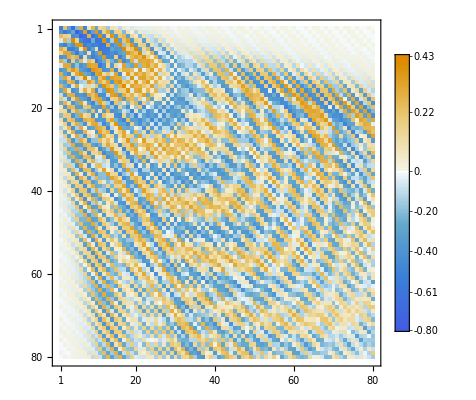

```mathematica
MatrixPlot[Commutator[SqueezeOperator[ξ1],DisplacementOperator[αcoh]]["Matrix"],PlotLegends->Automatic]
```

For a displaced squeezed state

When r → 0, the results for a coherent state are recovered, or when α → 0  the results of squeezed vacuum are recovered

```mathematica
dispSqueezed = DisplacementOperator[αcoh]@ SqueezeOperator[ξ1][];
```

```mathematica
{(QuantumMeasurementOperator[SuperDagger[a]@a]@ dispSqueezed)["Mean"],Abs[αcoh]^2 +Sinh[Abs[ξ1]]^2}
```

{1.9,1.9}

For this state it still holds   
That can be interpreted that the error ellipses keep their shape for any ξ, the center is displaced by α maintaining the ellipse shape

```mathematica
With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, {OperatorVariance[dispSqueezed,#]& /@ Through[YOperators[θ1]]//Chop,1/4{Exp[-2r],Exp[2r]}}]
```

{{0.0634566,0.984926},{0.0634566,0.984926}}

```mathematica
Module[{θ1=Arg[ξ1],dx ,dy, h=Re[αcoh], k = Im[αcoh]}, 
dx = OperatorVariance[dispSqueezed,YOperators[[1]][θ1]];dy =OperatorVariance[dispSqueezed,YOperators[[2]][θ1]] ;Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{h,k},{dx,dy}],θ1/2],
Black,Dashed,Line[#+{h,k}&/@Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],Line[#+{h,k}& /@ Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
],PointSize[0.022],Point[{h,k}],{Red,Dashing[1,0,0],Arrow[{{0,0},{h,k}}],Text["α",{0.05*h,0}+{h,k}/2]}},
Axes->True,Frame->True,ImageSize->Medium,AxesLabel->{"X1","X2"},PlotRange->{{-2,1},{-2,2}}]
]
```

-Graphics-

### More properties of squeezed states

For a squeezed vacuum state it can be shown mathematically that  the photon statistics only has non zero values for even number of photons

```mathematica
ξ1 = RandomReal[{1,2}]Exp[ⅈ RandomReal[{0,2Pi}]];
```

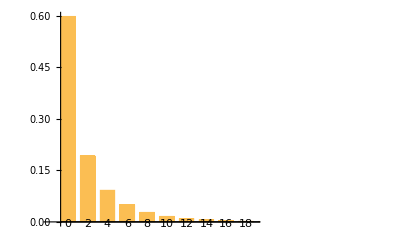

```mathematica
SqueezeOperator[ξ1][]["ProbabilityPlot",PlotRange->{{0,10.5},Automatic}]
```

Verifying the expansion in Fock basis:

```mathematica
Chop[With[{vals = AbsArg[ξ1]}, 1/(√Cosh[vals[[1]]])Table[(-1)^m(√((2m)!))/(2^m  m!)ⅇ^(ⅈ m vals[[2]]) Tanh[vals[[1]]]^m,{m,0,$FockSize/2-1}]]-SqueezeOperator[ξ1][]["AmplitudeList"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Generation of squeezed states

A common technique  to generate squeezed light is  to implement parametric processes with the aid of non linear optical devices. A non-linear medium  is pumped by a field of frequency ω_P and photons of the field are converted into pairs of signal photons each of frequency ω = ω_P/2. This is known as degenerate parametric down-conversion

where  b is the pump mode, a is the signal mode and  is the second order susceptibility

And we can make the approximation that the pump is in a really strong classical field, strong enough to never run out of photons. We can assume the field  is in  a coherent state |β e^(- ι ω_P t)⟩ and operator b and b^† are replaced by  β e^(- ⅈ ω_P t) and β^* e^(ⅈ ω_P t), so the Hamiltonian can be expressed as:

where

```mathematica
SetFockSpaceSize[40];
```

Time independent term:

```mathematica
H0PA = h ω SuperDagger[a]@a;
```

Time dependent term:

```mathematica
HIPA = ⅈ h (η* a@a ⅇ^(ⅈ Subscript[ω, P] t)-η  (SuperDagger[a]@SuperDagger[a] ⅇ^(-ⅈ Subscript[ω, P] t)));
```

Exponential of free part:

```mathematica
U =  Exp[-ⅈ H0PA/h t];
```

Going to the interaction picture:

```mathematica
HI = QuantumOperator[Simplify[SuperDagger[U]@ HIPA @ U,Element[{h,Subscript[ω, P],t,ω},Reals]],"Parameters"->{Subscript[ω, P],η}];
```

We get an interaction Hamiltonian , but we consider ω_P = 2 ω that is an energy conserving condition that Hamiltonian becomes time independent

```mathematica
FreeQ[HI[ω,η]["Amplitudes"]//Values,t]
```

False

```mathematica
FreeQ[HI[2ω,η]["Amplitudes"]//Values,t]
```

True

The evolution operator using that interaction Hamiltonian can be shown to take the form of a squeeze operator where ξ = 2 η t
We can check this applying the operators on the vacuum , for the sake of the example we take η = 1:

```mathematica
Table[QuantumSimilarity[Exp[-ⅈ HI[2ω,t]/h][],SqueezeOperator[2t,"Ordering"->"Weak"][]],{t,0.1,0.5,0.05}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Table[QuantumSimilarity[Exp[-ⅈ HI[2ω,t]/h][],SqueezeOperator[2t,"Ordering"->"Normal"][]],{t,0.1,0.5,0.05}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,0.999997}

## Detection of squeezed state : Homodyne detection

```mathematica
SetFockSpaceSize[40];
```

```mathematica
a1 = a;
a2 = QuantumOperator[a,{2}];
```

Using a balanced BS it can be proved :  
n_3-n_4 is related to the photocurrent difference which is an observable with direct experimental interpretation

```mathematica
i34 =ⅈ(SuperDagger[a2]@a1-SuperDagger[a1]@a2);
Xθ = QuantumOperator[1/2(a ⅇ^(-ⅈ θ)+ SuperDagger[a] ⅇ^(ⅈ θ)),"Parameters"->θ];
```

Given an input state which β being a coherent state and ψ any state :      
where ϕ is the phase of the complex β. We can define θ = ϕ - π/2 and quadrature at angle θ is defined  , to vary θ we vary ϕ and get different quadrature measurements. For the variances of the quadratures we get a similar formula

We try also  with a coherent state in the signal port, but has to be weaker than the local oscillator strong coherent field

Signal state:

```mathematica
αc = RandomComplex[];
ψ = coherent[αc];
```

Strong local field:

```mathematica
osciAmp = 3;
cohOsci = QuantumState[coherent[osciAmp Exp[I ϕ]]];
```

Total input state dependent on the phase of the local oscillator:

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->ϕ];
```

Calculating quadratures:

```mathematica
quadratures = Table[{x,(SuperDagger[in[x]]@i34 @ in[x])["Scalar"]/(2osciAmp)//Chop},{x,N@Subdivide[0,2Pi,40]}];
```

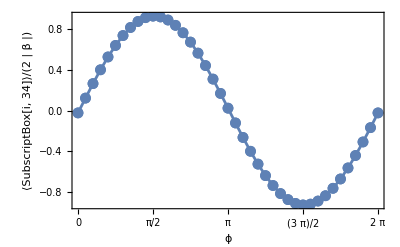

```mathematica
ListLinePlot[quadratures,Mesh->Full,FrameTicks->{{Automatic,None},{Range[0,2Pi,Pi/2],None}},FrameLabel->{"ϕ","⟨SubscriptBox[i, 34]⟩/(2  | β |)"},Frame->True,GridLines->{Range[0,2Pi,Pi/2],Range[-Abs[Im[αc]],Abs[Im[αc]],0.1]}]
```

For a coherent state we can extract the parameters easily, X(ϕ = 0) = X(θ = –π/2) = -X_2 , and X(ϕ = π/2) = X(θ = 0) = X_1
so the real and imaginary part of the α amplitude can be obtained

```mathematica
{Xθ[0] == QuadratureOperators[][[1]], Xθ[-π/2] == -QuadratureOperators[][[2]]}
```

{True,True}

```mathematica
{-Im[αc],quadratures[[1,2]]}
```

{-0.0233859,-0.0233859}

```mathematica
{Re[αc],quadratures[[Ceiling[(Length@quadratures/4)],2]]}
```

{0.931465,0.931465}

For a displaced squeezed state we can get the information about α with the means of ι_34 and information about ξ with the variances of the photo-current difference

Local oscillator:

```mathematica
osciAmp = 4;
cohOsci = QuantumState[coherent[osciAmp Exp[I ϕ]]];
```

```mathematica
ξ1 = 0.15 Exp[ⅈ RandomReal[{0,2π}]];
ψ = DisplacementOperator[αc]@SqueezeOperator[ξ1][];
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->ϕ];
```

Calculating quadratures expectations:

```mathematica
quadratures = Table[{x,(in[x]["Dagger"]@i34 @ in[x])["Scalar"]/(2osciAmp)//Chop},{x,N@Subdivide[0,2Pi,40]}];
```

```mathematica
ListLinePlot[quadratures,Mesh->Full,FrameTicks->{{Automatic,None},{Range[0,2Pi,Pi/2],None}},FrameLabel->{"ϕ","⟨SubscriptBox[i, 34]⟩/(2  | β |)"},Frame->True,GridLines->{Range[0,2Pi,Pi/2],Automatic}]
```

-Graphics-

Now we calculate the variances:

```mathematica
variances = Table[{x,OperatorVariance[in[x],N[i34]]/(4 osciAmp^2)//Chop},{x,N@Subdivide[0,2Pi,40]}];
```

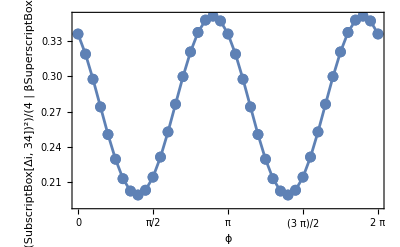

```mathematica
ListLinePlot[variances ,Mesh->Full,FrameTicks->{{Automatic,None},{Range[0,2Pi,Pi/2],None}},Frame->True,GridLines->{Range[0,2Pi,Pi/2],Automatic},FrameLabel->{"ϕ","(SubscriptBox[Δi, 34])^2/(4  | βSuperscriptBox[|, 2])"}]
```

Getting r (or a really close value) can get better using a stronger local oscillator:

```mathematica
NSolve[{Max[variances[[All,2]]]==1/4Exp[2 r]},r]//First
```

{r→0.170197}

```mathematica
Abs[ξ1]
```

0.15

Getting ϕ, for this one we can get really accurate because we extract from a fit using simulated values:

```mathematica
nlm =NonlinearModelFit[variances,k Sin[2(ϕ-α)]+c,{k,c,α},ϕ]
```

FittedModel[…]

```mathematica
2(α /. nlm["BestFitParameters"])-π/2
```

-0.643407

```mathematica
Arg[ξ1]
```

-0.643409

## Schrodinger cat states

Another important state with non classical properties are superpositions of classical-like states, which are a superposition of coherent states with equal amplitude magnitude but with a phase difference of π (α and -α)
 where 𝒩 is a normalization factor and we take α real
When |α| is large the states are macroscopically distinguishable  and the superpositions are called Schrodinger cat states( resembling the dead or alive state), which Schrodinger’s intention was to mock the Copenhagen interpretation of quantum mechanics. Nowadays, it is possible to consider quantum superpositions of macroscopically distinguishable states in an experimental setup. The reason we do not observe superpositions of macroscopic states its because a quantum system is not  completely isolated, so it interacts with the environment and as a result quantum superpositions decohere into statistical mixtures ( this topic will be discussed in the section of Dissipation and Decoherence). When |α| is greater the decay into a statistical mixture of the form   is faster, for now we will focus on the non-classical properties of these states.

Defining the general Schrodinger cat state, when ϕ = 0 the state is said to even cat states and when ϕ = π the state is an odd cat state. The case when ϕ = π/2 are called Yurke-Stoler states. These three cases  are eigenstates of (â)^2 with eigenvalue α^2

```mathematica
SetFockSpaceSize[20];
```

Lets visualize the photon distributions
Even cat state only have non zero amplitudes at even Fock states:

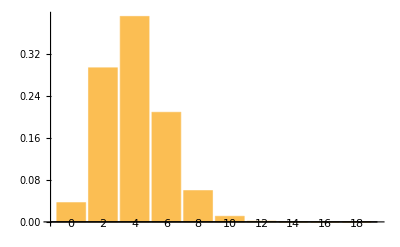

```mathematica
CatState[][2.,0]["ProbabilityPlot"]
```

Odd cat state only has odd photon Fock states:

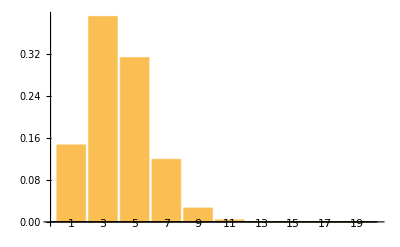

```mathematica
CatState[][2.,π]["ProbabilityPlot"]
```

For Yurke-Stoler the distribution is identical of a coherent state |α⟩ (the amplitudes are not the same though):

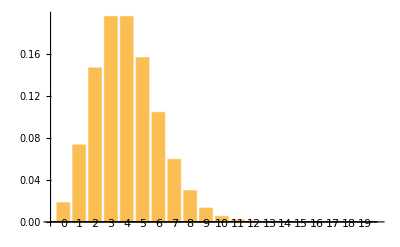

```mathematica
CatState[][2.,π/2]["ProbabilityPlot"]
```

```mathematica
Chop[CatState[][2.,π/2]["ProbabilityList"]-coherent[2.]["ProbabilityList"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The Mandel Q-parameter for even cat state is > 0 so has super-Poissonian statistics for all α, for the odd cat state is < 0 for all α  showing sub-Poissonian statistics. For the Yurke-Stoler state  obviously Q = 0 because it has photon distribution the same as a coherent state, when |α| is large  Q → 0 for both even and odd cat states.

```mathematica
MandelQParameter[ψ_QuantumState]:= With[{mean=(ψ["Dagger"]@SuperDagger[a]@a@ψ)["Scalar"]},(OperatorVariance[ψ,SuperDagger[a]@a]- mean)/mean]
```

```mathematica
Table[MandelQParameter@CatState[][αc,ϕ],{αc,{0.2,0.5,1.,1.5}},{ϕ,{0,π/2,π}}]//Chop
```

{{0.998934,0,-0.998934},{0.959517,0,-0.959517},{0.551441,0,-0.551441},{0.0999933,0,-0.0999933}}

Even cat states and Yorke-Stoler states present quadrature squeezing in X_2  (this holds for any α real)

```mathematica
αc = RandomReal[{0,2}];
```

```mathematica
TableForm[Table[Chop@OperatorVariance[CatState[][αc,ϕ],quad],{ϕ,{0,π,π/2}},{quad,QuadratureOperators[]}],TableHeadings->{{"Even cat","Odd cat","Yorke-Stoler"}, {"X_1","X_2"}}]
```

| X_1 | X_2
Even cat | 0.843445 | 0.112454
Odd cat | 1.20153 | 0.470543
Yorke-Stoler | 0.980992 | 0.210731

For the mixture   
 and ,   so there is clearly not squeezing  
For example for α = 2

```mathematica
statisticalMixture = 1/2coherent[2.]["MatrixState"]+1/2coherent[-2.]["MatrixState"];
```

```mathematica
With[{m =statisticalMixture["DensityMatrix"]}, Tr[(#@#)["Matrix"].m]- Tr[#["Matrix"].m]^2& /@ QuadratureOperators[]]
```

{4.25,0.25+0. ⅈ}

The quasi-probability distribution that can give more insight of the contrast of studied superpositions and statistical mixtures is the Wigner function, the Wigner function for the statistical mixture are two gaussian peaks centered at ± α . The Wigner function of the even cat state show a behavior that is oscillatory because of the interference of |α⟩ and |-α⟩, and also presents negative values that is a non-classical characteristic. The functions for the odd cat state and Yorke-Stoler are quite similar in behavior to the even cat state.

```mathematica
Block[{wig = WignerRepresentation[CatState[][2,0],{-4.5,4.5},{-4.5,4.5}]},
Plot3D[wig[x,p],{x,-4.5,4.5},{p,-4.5,4.5},
PlotRange->All,ColorFunction->"DarkRainbow",PlotLegends->Automatic,PlotPoints->100]]
```

-Graphics3D-

```mathematica
Block[{wig = WignerRepresentation[statisticalMixture,{-4.5,4.5},{-4.5,4.5}]},
Plot3D[wig[x,p],{x,-4.5,4.5},{p,-4.5,4.5},
PlotRange->All,ColorFunction->"DarkRainbow",PlotLegends->Automatic,PlotPoints->100]]
```

-Graphics3D-

## Two-mode squeezed vacuum states

We now consider squeezing with multimode fields and it is possible to have entanglement between the modes , such characteristics can exhibit more diverse non-classical effects. We will just explore the two mode case , defining the two mode squeeze operator and two mode squeezed vacuum:

Note the squeezed operator of two modes cannot be decomposed as a product of two single mode squeeze operator, hence it can be shown that the two mode squeezed state is entangled with correlations between the two modes

```mathematica
SetFockSpaceSize[30];
op1 = a["Bend"];
op2 = SuperDagger[a]["Bend"];
a1 = a;
b1 = QuantumOperator[a,{2}];
```

```mathematica
twoModesqueezeVacuum[ξ_?NumberQ]:= MatrixExp[(ξ* op1-ξ op2)][]
```

We can define quadrature operators for the two mode field

```mathematica
twomodeX1 := 1/2^(3/2)(a1+a1["Dagger"]+b1+b1["Dagger"])
twomodeX2 := 1/(2^(3/2) ⅈ)(a1-a1["Dagger"]+b1-b1["Dagger"])
```

It holds that  ⟨X_1⟩ = ⟨X_2⟩ = 0

```mathematica
ξ1 = RandomComplex[];
With[{state = twoModesqueezeVacuum[ξ1]}, (SuperDagger[state]@ # @ state)["Scalar"]& /@ {twomodeX1,twomodeX2}]
```

{0,0}

Like the single mode case the variances of X_1 and X_2 are

```mathematica
OperatorVariance[twoModesqueezeVacuum[ξ1],#]& /@{twomodeX1,twomodeX2}//Chop
```

{0.30509,1.77516}

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{0.305088,1.77517}

For θ = 0, we get the expressions we found before for the one mode case 1/4{Exp[-2r], Exp[2r]}:

```mathematica
OperatorVariance[twoModesqueezeVacuum[0.3],#]& /@{twomodeX1,twomodeX2}//Chop
```

{0.137203,0.45553}

```mathematica
{Exp[-2*0.3],Exp[2*0.3]}/4
```

{0.137203,0.45553}

The squeezed vacuum can be shown to be decomposed in the number state basis as

So this state is entangled with  strong correlations such that only the two mode Fock states |n,n⟩ appear

This plot shows the photon distribution for the two modes, using a squeeze parameter with r = 1.3

```mathematica
s2 = twoModesqueezeVacuum[1.3];
BarChart3D[ArrayReshape[s2["Probabilities"]//Values,{$FockSize,$FockSize}][[1;;15,1;;15]],]
```

-Graphics3D-

The modes are symmetric in their photon distribution ⟨n_a⟩ = ⟨n_b⟩ = sinh^2(r)

```mathematica
With[{state=twoModesqueezeVacuum[ξ1]},(state["Dagger"]@#@state)["Scalar"]& /@{a1["Dagger"]@a1,b1["Dagger"]@b1}]//Chop
Sinh[Abs[ξ1]]^2
```

{1.58026,1.58026}

1.58026

And the variances ⟨ (Δn_a)^2⟩= ⟨(Δn_b)^2⟩ = 1/4 sinh^2(r), it follows that both modes have super-Poissonian photon distributions

```mathematica
With[{state=twoModesqueezeVacuum[ξ1]},OperatorVariance[state,#]& /@{a1["Dagger"]@a1,b1["Dagger"]@b1}]//Chop
1/4 Sinh[2 Abs[ξ1]]^2
```

{4.07742,4.07742}

4.07749

If we consider a metric of entanglement like the RenyiEntropy, we can observe that the measure of entanglement increases with increasing r:

```mathematica
entanglementEntropies = Table[{r,QuantumEntanglementMonotone[twoModesqueezeVacuum[r],"RenyiEntropy"]},{r,0.,1.5,0.05}];
```

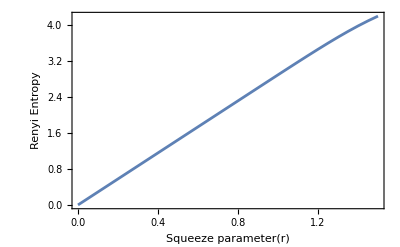

```mathematica
ListLinePlot[entanglementEntropies,Frame->True,FrameLabel->{"Squeeze parameter(r)","Renyi Entropy"},LabelStyle->13]
```

## Paclet installation

Install  the Quantum Framework paclet:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Load quantum framework functions:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load quantum framework functions for the second quantization:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
coherent := CoherentState[]["Normalize"];
```